# Wolfram Language Tutorial

## Jovana Andrejevic, Nina Andrejevic, and George Varnavides

## Following along

```mathematica
URLShorten["https://raw.githubusercontent.com/gvarnavi/generative-art-iap/master/Tutorials/00_wolfram-language-tutorial.nb"]
```

https://wolfr.am/SCw8Labv

```mathematica
NotebookOpen["https://wolfr.am/SCw8Labv"]
```

83a2z_shm19FrontEndObject[LinkObject["83a2z_shm", 3, 1]]1901_Introduction[1].nbC:\Users\George Varnavides\AppData\Local\Microsoft\Windows\INetCache\IE\DBWG7NH1\01_Introduction[1].nb

## General Use

### Easiest start: natural language input

“= plot x^2 from -5 to 5”

WolframAlphaQueryParseResults

### Working in a notebook

Shift+Enter!

```mathematica
variable
```

```mathematica
variable=134
```

The most recently assigned definition prevails regardless of order:

```mathematica
variable=16
```

Combine text, images, and working code in one notebook.

```mathematica
default (*comment*)
```

## Documentation

### Mathematica has thousands of built-in functions

```mathematica
?Graphics
```

```mathematica
?Graph*
```

```mathematica
?*Graph*
```

## General Syntax

### Functions

Generally: FunctionName[arg1, arg2, ...optArg, opt1→True, opt2→False]
Arguments are ordered; options are not

```mathematica
Plot[ x^2,{x, -5, 5},
PlotRange->{0,1},
PlotStyle->{Thick,Red},
Frame->True]
```

You try: plot x^3 from 0 to 1 in a new color

#### Alternative function notation (entirely optional, but you’ll probably see it around):

```mathematica
f[x] (*standard notation*)
```

```mathematica
f@x(*prefix notation*)
```

```mathematica
x//f(*postfix notation*)
```

```mathematica
x~f~y (*infix notation*)
```

### Lists

Generally: {e1, e2, e3}

Mathematica uses 1-indexing!

#### Index specific elements with [[]]:

one element: [[ i ]]
	set of elements: [[ {i, j, k} ]]
	range of elements: [[ i ;; j ]]
	backwards from the end: [[ -i ]]

```mathematica
{1,2,3,4,5,6,7,8}[[1]]
```

### Graphics

Generally: Graphics[{style1, style2, object1, object2}, options]

```mathematica
Graphics[{Blue, Thick, Circle[{-1,1},1],Orange, Rectangle[{-1,1},{0,2}]},ImageSize->Small]
```

You try: recreate the graphic below (hint: filled circle = Disk[])

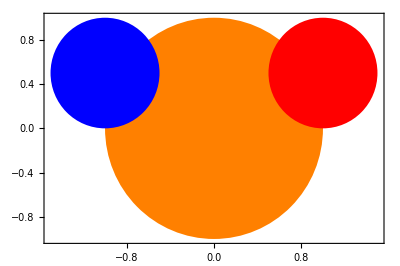

```mathematica
Graphics[{Orange, Disk[{0,0},1], Blue, Disk[{-1,0.5},0.5], Red, Disk[{1,0.5}, 0.5]}, Frame->True]
```

## Working with Lists

### Writing lists

Write an arithmetic sequence of numbers: use Range

```mathematica
Range[10,0,-2]
```

Write lists with a more complicated rule: use Table (a Mathematica version of a For Loop)

```mathematica
Table[4*n-2,{n,0,10}]
```

### Expanding lists

Return a list with an element added to the end: use Append

```mathematica
Append[Range[0,10],12]
```

Return a list with an element added to the end AND reset its definition: use AppendTo

```mathematica
AppendTo[Range[0,10],12]
```

```mathematica
list1=Range[0,10];
AppendTo[list1, 12];
list1
```

{0,1,2,3,4,5,6,7,8,9,10,12}

The functions Prepend and PrependTo add elements to the beginning of a list

### Grouping list elements

Find all possible ordered combinations of a list: use Tuples

```mathematica
Tuples[Range[6],2]
```

You can use Subsets if order doesn't matter

```mathematica
Subsets[Range[6], {2}]
```

Divide a list into sublists of a given length: use Partition

```mathematica
Partition[Range[1,10],2]
```

Recombine sublists into one big list: use Flatten (this is useful if you have extra parentheses around a list)

```mathematica
Flatten[Partition[Range[1,10],2]]
```

You try: list the set of odd integers from 1 to 23, then divide into sublists of length 3

## Writing Your Own Functions

### Standard form

```mathematica
sumFunction[var1_, var2_]:=var1+var2
```

^function name
		    ^ set of arguments with underscores
		     				 ^ : = is a “set delay”; function is evaluated  each time it’s called
		     				 	^ function behavior: what happens to the arguments?

```mathematica
sumFunction[1,2]
```

You try: write a function that picks randomly between three inputs (hint: it makes a RandomChoice)

#### Optional arguments

Your functions can have optional arguments:

```mathematica
addMaybe5[n1_, n2_:5]:=n1+n2
```

```mathematica
addMaybe5[2]
```

```mathematica
addMaybe5[2,3]
```

#### Alternate function input forms

The same function can accommodate multiple input styles:

```mathematica
flexibleForm[{a_,b_},c_]:="tuple first"
```

```mathematica
flexibleForm[c_,{a_,b_}]:="number first"
```

### Mapping over inputs

If you want to apply your function to a whole list of inputs, you can Map

```mathematica
square[n_]:=n^2
```

```mathematica
Map[square, Range[0,5]]
```

Fancy syntax: /@

```mathematica
square/@Range[0,5]
```

### Pure functions (optional, but you’ll see them being used)

If you’re only going to use a function in a single context, you don’t need to define it outside of that context.
Instead, you can use a pure function

```mathematica
#^2&
```

The # is called a slot, and it shows where the input is supposed to go
The & is a label that indicates a pure function is being used

```mathematica
Map[#^2&, Range[0,5]]
```

Very terse syntax:

```mathematica
#^2&/@Range[0,5]
```

You try: write a pure function that triples its input, and apply it to integers -3 to 3

## Working with Graphics

### The Graphics wrapper

A list of objects within a Graphics wrapper will be evaluated left → right and all shown together
Options can be added after the list in any order

```mathematica
Graphics[{Purple, Disk[{0,0},0.5],Blue, Disk[{1,0},0.5], Green, Disk[{2,0},0.5],Disk[{3,0},0.5]},Frame->True]
```

```mathematica
Graphics[{{Purple, Disk[{0,0},0.5]},{Blue, Disk[{1,0},0.5]}, Disk[{2,0},0.5],Disk[{3,0},0.5]},Frame->True]
```

### Functions with Graphics

Functions can be written to draw graphics programmatically

```mathematica
Graphics[
Disk[#, 0.5]&/@Tuples[Range[0,4],2]
]
```

```mathematica
Graphics[
{Hue[EuclideanDistance[{2,2},#]/5],
Disk[#, 0.25]}&/@Tuples[Range[0,4,0.5],2]
]
```

### Colors

Standard colors (RGBIV, CMYK, white, and gray) can be specified by name:

```mathematica
{White,Magenta,Red, Orange, Yellow, Green,Cyan, Blue, Purple, Black, Gray, LightGray}
```

RGB colors can also be specified

```mathematica
RGBColor[0.31,0.63,1.]
```

Hue can be used to convert numbers 0→1 into rainbow tones

```mathematica
Table[Hue[n], {n, 0, 1, 0.05}]
```

ColorData gives many ready-made color palettes, which can be used like Hue (shown in Color Schemes in the documentation)

```mathematica
ColorData["Gradients"]
```

```mathematica
Table[ColorData["ThermometerColors"][n], {n, 0, 1, 0.05}]
```

## Dynamic Outputs

### Dynamic

Dynamic allows an output to change as it’s recomputed in real time

```mathematica
i=0;
```

```mathematica
i
```

```mathematica
i+=1;
```

```mathematica
Dynamic[Graphics[{Hue[i],Disk[]}]]
```

```mathematica
Do[i+=0.01;Pause[0.05], 100]
```

### Animate

Animate visualizes data and relationships in a “movie-like” or “.gif-like” manner

```mathematica
Animate[Graphics[{Hue[i], Disk[]}], {i, 0,1,0.01}]
```

### Manipulate

Manipulate allows a user to manually sweep through data

```mathematica
Manipulate[Graphics[{Hue[i], Disk[]}], {i, 0,1,0.01}]
```

## Nesting

### Fractal-like behavior is often the result of nesting

Nesting means that a function’s output is fed back into the same function as input

The set of “Nest...” functions should cover all of your nesting needs

```mathematica
function[function[function[x]]]
```

```mathematica
Nest[function, x, 3]
```

Let’s write a function to add 3 to the input: (yes, this is a lame example)

```mathematica
add3[input_]:=input+3
```

```mathematica
Nest[add3, 1, 3]
```

List all outputs with NestList

```mathematica
NestList[add3, 1, 3]
```

Keep going until a condition is met with NestWhile

```mathematica
NestWhile[add3, 1, #<100&]
```

List all outputs until a condition is met with NestWhileList

```mathematica
NestWhileList[add3, 1, #<100&]
```

List all outputs until the outputs converge with FixedPoint or FixedPointList

```mathematica
FixedPointList[(#+2/#)/2&,1.]
```

You try: write a function that will double its input. Starting from 1, nest the function until the output exceeds 200. 
If you plot your results, they should look like this:

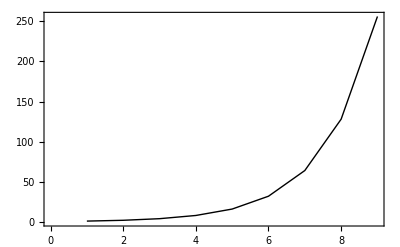

```mathematica
ListLinePlot[NestWhileList[2*#&, 1, #<200&], Frame->True, PlotStyle->{Black, Thick}]
```